```mathematica
Plot3D[Cos[x]+Sin[y],{x,0,4π},{y,0,4π}]
```

```mathematica
Plot3D[Cos[x]+Sin[y],{x,0,4π},{y,0,4π},
RegionFunction->Function[{x,y,z},z>0],
BoxRatios->{2π,2π,2}
]
```

```mathematica
Plot3D[Cos[x]+Sin[y],{x,-π,π},{y,-π/2,3 π/2},
RegionFunction->Function[{x,y,z},z≥0],
BoxRatios->{2π,2π,2}
]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x]+Sin[y],{x,-π,π},{y,-π/2,(3π)/2},
RegionFunction->Function[{x,y,z},z≥0 &&(x<0||y>3 π/4)],
BoxRatios->{2π,2π,2}
]
```

-Graphics3D-

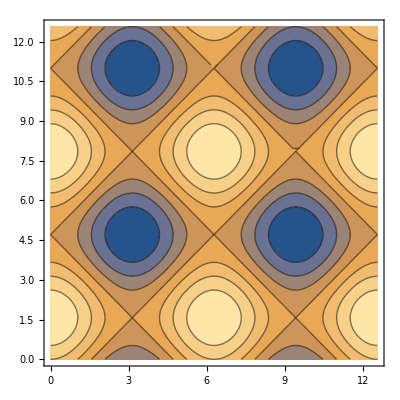

```mathematica
ContourPlot[Cos[x]+Sin[y],{x,0,4π},{y,0,4π}]
```

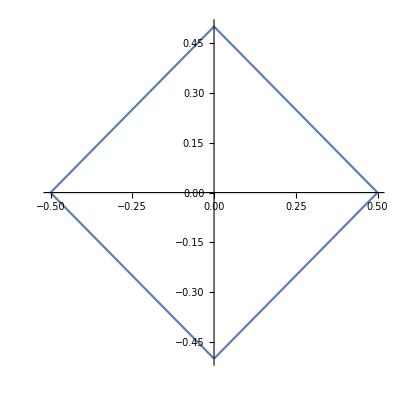

```mathematica
ParametricPlot[
{1/2-Abs[Mod[t,2]-1],1/2-Abs[Mod[1/2+t,2]-1]},
{t,0,2}
]
```

```mathematica
r=1;
Manipulate[
RevolutionPlot3D[
{r+(1/2-Abs[-1+Mod[t,2]])Cos[θ]-(1/2-Abs[-1+Mod[1/2+t,2]])Sin[θ],
(1/2-Abs[-1+Mod[1/2+t,2]])Cos[θ]+(1/2-Abs[-1+Mod[t,2]])Sin[θ]
},
{t,0,2},PerformanceGoal->"Quality"
],
{θ,0,π/2}
]
```